```mathematica
0.5(11100/5000)+8.9
```

10.01

```mathematica
<<Units`
```

```mathematica
Convert[1 Pound/Gallon,1 Kilogram/Meter^3]
Convert[1. Feet/Second^2,1 Meter/Second^2]
Convert[1 Feet,1Inch]
Convert[1 Gallon,1Inch^3]
```

(119.826 Kilogram)/Meter^3

(0.3048 Meter)/Second^2

12 Inch

231. Inch^3

```mathematica
12/231.
```

0.0519481

0.0126949

```mathematica
ComputeBurstPressure[L_,MudWeigthToFrac_,MudWeigthToKick_,GasGrad_]:=Block[{SF=0.5,PI(*InjectionPressure*),SHP(*SurfaceHolePressure*),BHP(*BottomHolePressure*)},
PI=0.052 (MudWeigthToFrac+SF)L;
SHP=PI-GasGrad L;
BHP=PI-MudWeigthToKick L 0.052;
{SHP,BHP}
];
```

```mathematica
ComputeBurstPressure[5000,14.76,8.95,0.1]
```

{3467.6,1640.6}

```mathematica
0.465/0.052
```

8.94231

```mathematica
(14.76+0.5)0.052 5000
```

3967.6

```mathematica
LinearEq[input_]:=Block[{y,x,temp,temp2,temp3,pt1,pt2},
pt1=input[[1]];
pt2=input[[2]];
temp=(pt2[[2]]-pt1[[2]])/(pt2[[1]]-pt1[[1]])(x-pt1[[1]])+pt1[[2]];
(*temp2=temp/.x->pt1[[1]];
temp3=temp/.x->pt2[[1]];
y=Piecewise[{{pt1[[1]],temp2>0},{pt2[[1]],temp3<pt2[[2]]}},temp];*)
Return[temp]
]
```

```mathematica
13.1 1.1
```

14.41

```mathematica
(* 1 - Outside diameter(in) | 2 - Nominal weight(lb/ft) | 3 - Grade | 4 - Wall thickness (in) | 5 - Inside diameter (in) | 6 - Pipe collapse resistance (psi) | 7 - Body yield strength (1000 lbf) | 8 - Coupling type | 9 - Internal pressure resistance (psi) | 10 - Joint strength (1000 lbf) *)
PipesTable={
{20,       94,   K55,0.438,19.124,520,  1480,LTC,2110,955 },
{20,       133,K55,0.635,18.730,1500,2125,BTC,3036,2123},
{20,        65,   K55,0.375,15.250,630,  1012,STC,2260,625},
{16,        75,   K55,0.438,15.124,1020,1178,STC,2630,752},
{16,        84,   L80,0.495,15.010,1480,1929,BTC,4330,1861},
{16,        109, K55,0.656,14.688,2560,1739,BTC,3950,1895},
{13.375,98,  L80,0.719,11.937,5910,2800,BTC,7530,2286},
{13.375,85, P110,0.608,12.159,4690,2682,PTC,8750,2290},
{13.375,98, P110,0.719,11.937,7280,3145,PTC,10350,2800},
{9.625, 58.4,L80,0.595,8.435,7890,1350,BTC,8650,1396},
{9.625, 47,   P110,0.472,8.681,5310,1493,LTC,9449,1213},
{7,          38,V150,0.540,5.920,19240,1644,EXTL,18900,1430},
{7,          41,V150,0.590,5.820,22810,1782,PTC,20200,1052},
{7,          46,V150,0.670,5.660,25970,1999,PTC,25070,1344},
{7,          38,MW155,0.540,5.920,19700,1697,EXTL,20930,1592},
{7,          46,SOO140,0.670,5.660,24230,865,PTC,23400,1222},
{7,          46,SOO155,0.670,5.660,26830,2065,PTC,25910,1344}
};
```

```mathematica
SelecPipe[BurstCoords_,ColapseCoords_,CaseOD_,CaseLength_]:=Block[{plot={},i,eq1,eq2,CSF=0.85,BSF=1.1,sz,PipeLengthColapse,PipeLengthBurst,PCR,PBR,vecBurstLength={},vecColapseLength={},tolerance=0.1,grade,coupling,weight,OD},

eq1=LinearEq[BurstCoords];
eq2=LinearEq[ColapseCoords];

sz=Length[PipesTable];
For[i=0,i≤sz,i++,

If[Abs[(CaseOD-PipesTable[[i]][[1]])]<tolerance,

PBR=PipesTable[[i]][[9]] ;
PCR=PipesTable[[i]][[6]] ;
PBR=PBR /BSF;
PCR=PCR /CSF;
If[PBR>=BurstCoords[[1,1]],
PipeLengthBurst=BurstCoords[[1,1]];
,
PipeLengthBurst=-eq1/.x->PBR;
];

If[PCR>=ColapseCoords[[2,1]],
PipeLengthColapse=ColapseCoords[[2,1]];
,
PipeLengthColapse=-eq2/.x->PCR;
];

OD=PipesTable[[i]][[1]];
grade=PipesTable[[i]][[3]];
weight=PipesTable[[i]][[2]];
coupling=PipesTable[[i]][[8]];
(*If[PipeLengthColapse>PipeLengthBurst,
delta=PipeLengthColapse-PipeLengthBurst;
interval1=PipeLengthBurst+delta;
interval2=CaseLength-interval1;
Print[" OD = ",OD,"|| grade = ",grade,"|| coupling = ",coupling," || weight = ",weight," || interval1 = ",interval1," || interval2 = ",interval2," || interval1+interval2 = ",interval1+interval2];
];
*)
Print["PipeLengthBurst = ",PipeLengthBurst];
Print["PipeLengthColapse = ",PipeLengthColapse];
AppendTo[plot,ContourPlot[{eq1==y,eq2==y,x==PBR,x==PCR,y==-PipeLengthBurst,y==-PipeLengthColapse},{x,0,CaseLength},{y,0,-CaseLength},AspectRatio->Automatic]];
];

];

Table[Show[plot[[i]]],{i,1,Length[plot]}]

];
```

Part::partd: Part specification List ⟦ 1 ⟧ is longer than depth of object.

PipeLengthBurst = 2974.5

PipeLengthColapse = 2429.15

OD = 16|| grade = L80|| coupling = BTC || weight = 84 || interval1 = 3524.65 || interval2 = 1475.35 || interval1+interval2 = 5000.

PipeLengthBurst = 3476.6

PipeLengthColapse = 3524.65

PipeLengthBurst = 3476.6

PipeLengthColapse = 2470

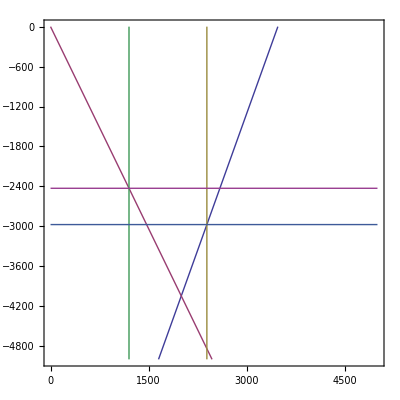
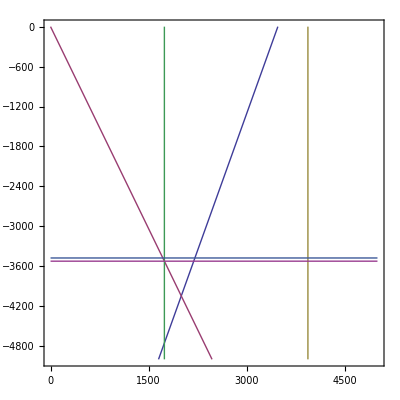
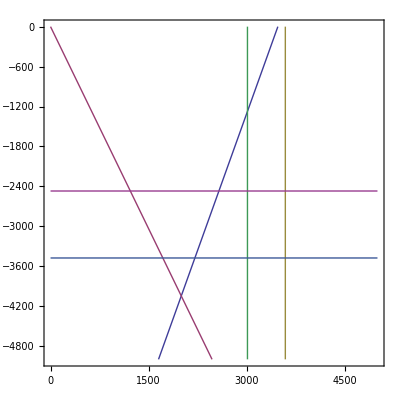

```mathematica
SelecPipe[{{3476.6,0},{1651.6,-5000}},{{0,0},{2470,-5000}},16,5000]
```